## Kerr metric

The metric for a black hole with mass M and angular momentum J in Boyer-Lindquist coordinates (t,r,θ,ϕ) is

ds^2==-(1-(r_s r)/Σ)dt^2+Σ/Δ dr^2+Σ dθ^2+(r^2+a^2+(r_s r a^2)/Σ Sin^2[θ])Sin^2[θ]dϕ^2-(2 r_s r a Sin^2[θ])/Σ dt dϕ ,

where

r_s==2 G_N M,    a==J/M,    Σ==r^2+a^2 Cos^2[θ]    and    Δ==r^2-r_s r+a^2 .

The inner and outer surfaces of the ergosphere and inner and outer (event) horizons are located at

r_E^±==r_s/2±√((r_s/2)^2-a^2 Cos^2[θ]),    r_H^±==r_s/2±√((r_s/2)^2-a^2) .

From this we find the extremality bound, (|a|)/(G_N M)==(|J|)/(G_N M^2)≤1. It will be useful to work in units where G_N M==1, so that r_s==2 and a∈[-1,1].

```mathematica
Σ[r_,θ_,a_]:=r^2+a^2 Cos[θ]^2;
Δ[r_,a_]:=r^2-2r+a^2;
```

### Conserved quantities and null geodesics

There are two ‘obvious’ conserved quantities associated to the Killing vectors ∂_t  and ∂_ϕ , which are the energy E==-p_t and angular momentum L_z==-p_ϕ. There is a third conserved quantity, the Carter constant Q==p_θ^2-Cos^2[θ](a^2 E^2-L_z^2 Csc^2[θ]), which is associated to a Killing tensor. These three constants, along with p_μ p^μ==0, are enough to determine a geodesic uniquely.

With affine parameter λ (so that (ⅆ x^μ)/ⅆλ==p^μ), trajectories are found by solving the following,

Σ ⅆr/ⅆλ==±√R[r]
Σ ⅆθ/ⅆλ==±√Θ[θ]
Σ ⅆϕ/ⅆλ==-(a E-L_z Csc^2[θ])+a/Δ P[r]
Σ ⅆt/ⅆλ==-a(a E Sin^2[θ]-L_z)+(r^2+a^2)/Δ P[r]

where the ‘potentials’ are

P[r]==E(r^2+a^2)-a L_z
Θ[θ]==Q+Cos^2[θ](a^2 E^2-L_z^2 Csc^2[θ])
R[r]==P[r]^2-Δ(Q+(a E-L_z)^2)

```mathematica
dtdλ[r_,θ_,a_,e_,Lz_,Q_]:=(-a^2 e Sin[θ]^2+a Lz+(r^2+a^2)/Δ[r,a] P[r,a,e,Lz])/Σ[r,θ,a];
drdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=signr (√R[r,a,e,Lz,Q])/Σ[r,θ,a];
dθdλ[r_,θ_,a_,e_,Lz_,Q_,signθ_]:=signθ (√Θ[θ,a,e,Lz,Q])/Σ[r,θ,a];
dϕdλ[r_,θ_,a_,e_,Lz_,Q_]:=(-a e+Lz Csc[θ]^2+a/Δ[r,a] P[r,a,e,Lz])/Σ[r,θ,a];
```

```mathematica
P[r_,a_,e_,Lz_]:=e(r^2+a^2)-a Lz;
Θ[θ_,a_,e_,Lz_,Q_]:=Q+Cos[θ]^2(a^2 e^2-Lz^2 Csc[θ]^2);
R[r_,a_,e_,Lz_,Q_]:=P[r,a,e,Lz]^2-Δ[r,a]((a e-Lz)^2+Q);
```

v==t+T[r], where T'[r]==(r^2+a^2)/Δ
φ==ϕ+Φ[r], where Φ'[r]==a/Δ

```mathematica
T[r_]:=r+1/2 Log[Δ[r,a]^2/16]+1/(2 √(1-a^2))Log[((r-(1+√(1-a^2)))/(r-(1-√(1-a^2))))^2];
Φ[r_]:=a/(4 √(1-a^2))Log[((r-(1+√(1-a^2)))/(r-(1-√(1-a^2))))^2];
```

```mathematica
Clear[a]
T'[r]==(r^2+a^2)/Δ[r,a]//Simplify
Φ'[r]==a/Δ[r,a]//Simplify
```

True

True

```mathematica
dvdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=dtdλ[r,θ,a,e,Lz,Q]+(r^2+a^2)/Δ[r,a] drdλ[r,θ,a,e,Lz,Q,signr];
dφdλ[r_,θ_,a_,e_,Lz_,Q_,signr_]:=dϕdλ[r,θ,a,e,Lz,Q]+a/Δ[r,a] drdλ[r,θ,a,e,Lz,Q,signr];
```

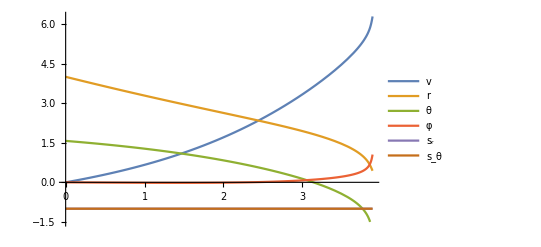

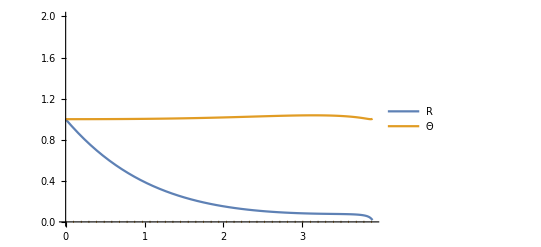

-Graphics3D-

```mathematica
a=3/4;

v0=0;
r0=4;
θ0=π/2;
φ0=0;

e=1;
Lz=0;
Q=15;

λmax=25;

eqns=Simplify@{
v'[λ]==dvdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]],
r'[λ]==drdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]],
θ'[λ]==dθdλ[r[λ],θ[λ],a,e,Lz,Q,signθ[λ]],
φ'[λ]==dφdλ[r[λ],θ[λ],a,e,Lz,Q,signr[λ]]
};
init={v[0]==v0,r[0]==r0,θ[0]==θ0,φ[0]==φ0,signr[0]==-1,signθ[0]==-1};

soln=First@NDSolve[{eqns,init,
WhenEvent[r[λ]≤(1-√(1-a^2))+10^-1,"StopIntegration"],
WhenEvent[R[r[λ],a,e,Lz,Q]<0.0001,{r[λ]->r[λ]-signr[λ]0.00001,signr[λ]->-signr[λ]}],
WhenEvent[Θ[θ[λ],a,e,Lz,Q]<0.0001,{θ[λ]->θ[λ]-signθ[λ]0.00001,signθ[λ]->-signθ[λ]}]
},
{v,r,θ,φ,signr,signθ},{λ,0,λmax},DiscreteVariables->{signr,signθ}];
domain=(r/.soln)["Domain"][[1,2]];

Plot[Evaluate[{v[λ],r[λ],θ[λ],φ[λ],signr[λ],signθ[λ]}/.soln],{λ,0,domain},PlotRange->{-1.5,Automatic},PlotLegends->{"v","r","θ","φ","s_r","s_θ"}]
ReImPlot[Evaluate[{R[r[λ],a,e,Lz,Q]/R[r0,a,e,Lz,Q],Θ[θ[λ],a,e,Lz,Q]/Θ[θ0,a,e,Lz,Q]}/.soln],{λ,0,domain},PlotRange->{0,2},PlotLegends->{"R","Θ"}]

r[λ]{Sin[θ[λ]]Cos[φ[λ]-0Φ[r[λ]]],Sin[θ[λ]]Sin[φ[λ]-0Φ[r[λ]]],Cos[θ[λ]]}/.soln;
Show[ParametricPlot3D[Chop[%],{λ,0,domain},PlotRange->{{-4,4},{-4,4},{-4,4}}],ParametricPlot3D[{(1+√(1-a^2)){Sin[th]Cos[ph],Sin[th]Sin[ph],Cos[th]},(1-√(1-a^2)){Sin[th]Cos[ph],Sin[th]Sin[ph],Cos[th]}},{th,0,π},{ph,0,2π},PlotStyle->{Directive[Red,Opacity[0.1]],Green},WorkingPrecision->20]]
```